```mathematica
Fp[s_]=1/(1-s/0.6870);
Φ[z_,η_,s_]=6*z*(1-z)*(2η-1)*Fp[s];
ph[t_,ξ_]=Φ[(x/ξ+1)/2,(y/ξ+1)/2,t];
(*ERBL-gpd part*)
Hqz1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*0.838*β^(0.7-1)(1-β)^2.03(1+13.8 β^2)/(1-t/0.6870);
Hqz2=(Hqz1/.{α->(x-β)/ξ})/ξ;
Hqzn2[x_,ξ_,t_]=Hqz2/.{b0->2,ξ->ξ/y,x->x/y};
(*DGLAPpart*)
Hq1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*0.838*β^(0.7-1)(1-β)^2.03(1+13.8 β^2)/(1-t/0.6870);
Hqa=(Hq1/.{α->(x-β)/ξ})/ξ;
Hqay[x_,ξ_,t_]=Hqa/.{b0->2,ξ->ξ/y,x->x/y};
```

```mathematica
dglap[x_]=Hqa/.{b0->2,ξ->0.1,t->0};
erbl[x_]=Hqz2/.{b0->2,ξ->0.1,t->0};
```

```mathematica
ind[x_]:=NIntegrate[dglap[x],{β,(x-0.1)/(1-0.1),(x+0.1)/(1+0.1)}];
ine[x_]:=NIntegrate[erbl[x],{β,0,(x+0.1)/(1+0.1)}];
```

```mathematica
ind[0.3]
```

1.30845

```mathematica
l1=ParallelTable[{x,ind[x]},{x,0.1,1,0.01}];
l2=ParallelTable[{x,ine[x]},{x,-0.1,0.1,0.001}];
```

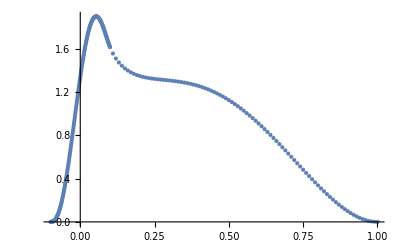

```mathematica
ListPlot[Join[l2,l1]]
```

```mathematica
(*D term*)
Dterm[x_,ξ_,t_]=(15*(0.793-1)/(2*(1-t/1.9^2)^3))*(x/ξ)*(1-(x/ξ)^2);
```